```mathematica
K2meV=0.086173324;
K2eV=K2meV/1000;
```

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/RESULTS_tom_17July17/FREN/order3"];
fileFFE={"e0.out.m","e0_fs.out.m","VFE.Fqh_FS.out.m","VFE.Fel_Fqh_FS.out.m"};
FFEdata=Table[ReadList[fileFFE[[i]],{Number, Number,Number,Number,Number,Number}],{i,1,4}];
```

```mathematica
32*31/2
```

496

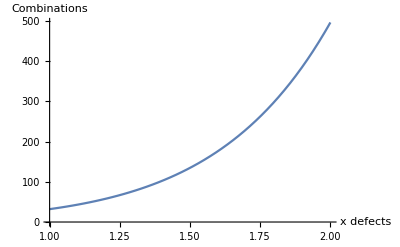

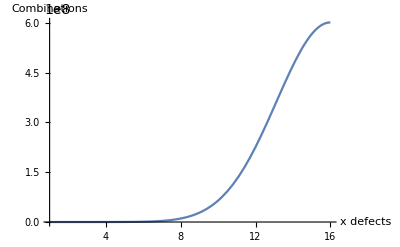

```mathematica
(*How many ways can I count x defects on 32 sites*)
f[x_]:=32!/((32-x)!*x!)
Plot[f[x],{x,1,2},AxesLabel->{"x defects","Combinations"}]
Plot[f[x],{x,1,16},AxesLabel->{"x defects","Combinations"}]
```

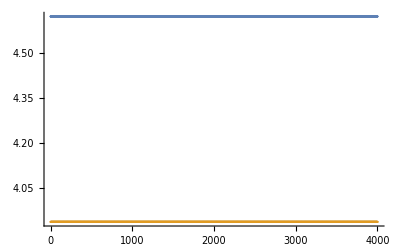

```mathematica
ListPlot@Transpose[FFEdata[[1]]][[2;;3]]
```

```mathematica
(*T_Kelvin FREN_1126_eVperD FREN_129_eVperD FREN_142_eVperD FREN_174_eVperD FREN_70_eVperD*)

(*1=1126=U4, 2=129=B2, 3=142=B3, 4=174=U3,5=70=U2 *)
```

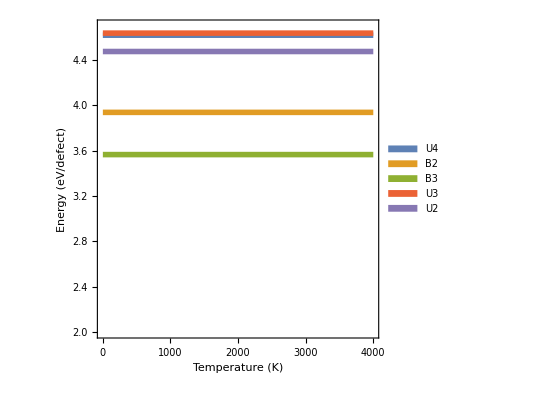

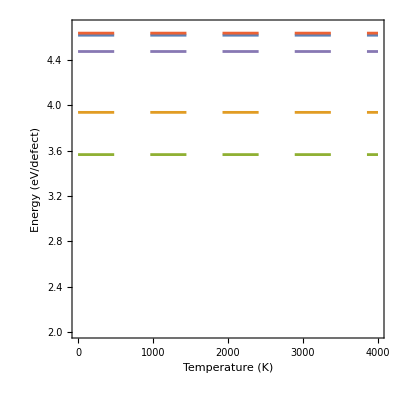

```mathematica
G1=ListLinePlot[Transpose[FFEdata[[1]]][[2;;6]],PlotRange->{Automatic,{2,4.7}},FrameLabel->{Style["Temperature (K)",18,Black],Style["Energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Thickness[0.01],FrameTicksStyle->18,Frame->True,ImageSize->400,PlotLegends->SwatchLegend[{Style["U4",20,Black],Style["B2",20,Black],Style["B3",20,Black],Style["U3",20,Black],Style["U2",20,Black]}]]
G1a=ListLinePlot[Transpose[FFEdata[[1]]][[2;;6]],PlotRange->{Automatic,{2,4.7}},FrameLabel->{Style["Temperature (K)",18,Black],Style["Energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Directive[Thickness[0.005],Dashing[0.065]],FrameTicksStyle->18,Frame->True,ImageSize->400]
```

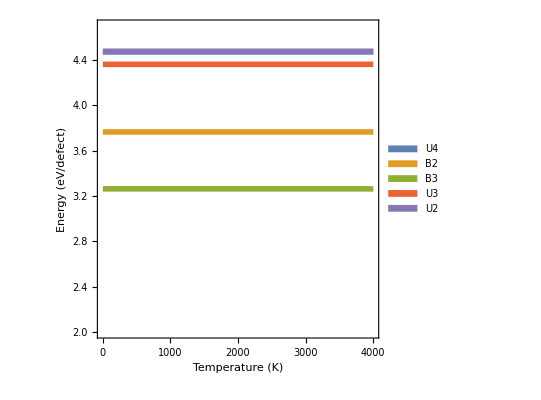

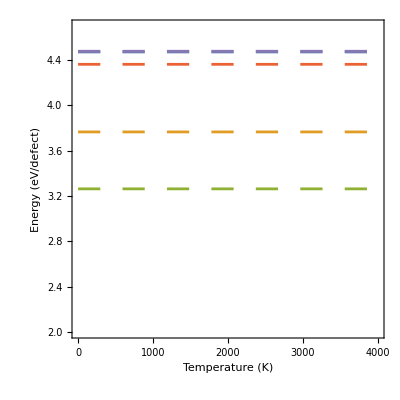

```mathematica
G2=ListLinePlot[Transpose[FFEdata[[2]]][[2;;6]],PlotRange->{Automatic,{2,4.7}},FrameLabel->{Style["Temperature (K)",18,Black],Style["Energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Thickness[0.01],FrameTicksStyle->18,Frame->True,ImageSize->400,PlotLegends->SwatchLegend[{Style["U4",20,Black],Style["B2",20,Black],Style["B3",20,Black],Style["U3",20,Black],Style["U2",20,Black]}]]
G2a=ListLinePlot[Transpose[FFEdata[[2]]][[2;;6]],PlotRange->{Automatic,{2,4.7}},FrameLabel->{Style["Temperature (K)",18,Black],Style["Energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Directive[Thickness[0.005],Dashing[0.04]],FrameTicksStyle->18,Frame->True,ImageSize->400]
```

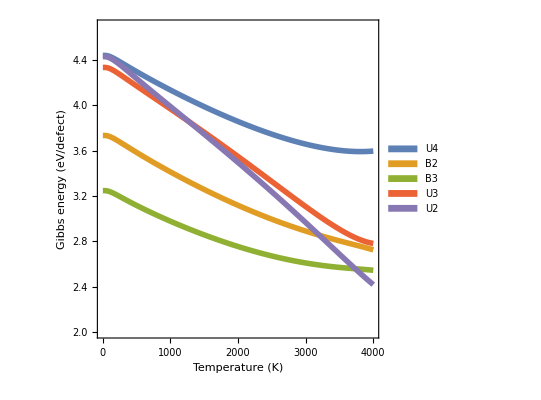

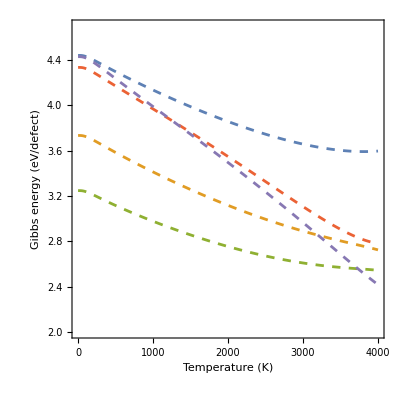

```mathematica
G3=ListLinePlot[Transpose[FFEdata[[3]]][[2;;6]],PlotRange->{Automatic,{2,4.7}},FrameLabel->{Style["Temperature (K)",18,Black],Style["Gibbs energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Thickness[0.01],FrameTicksStyle->18,Frame->True,ImageSize->400,PlotLegends->SwatchLegend[{Style["U4",20,Black],Style["B2",20,Black],Style["B3",20,Black],Style["U3",20,Black],Style["U2",20,Black]}]]
G3a=ListLinePlot[Transpose[FFEdata[[3]]][[2;;6]],PlotRange->{Automatic,{2,4.7}},FrameLabel->{Style["Temperature (K)",18,Black],Style["Gibbs energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Directive[Thickness[0.005],Dashing[0.015]],FrameTicksStyle->18,Frame->True,ImageSize->400]
```

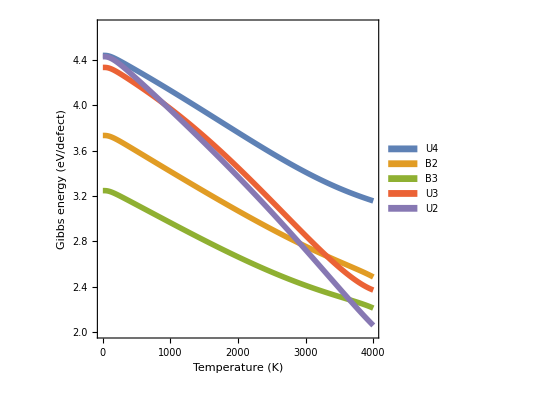

```mathematica
G4=ListLinePlot[Transpose[FFEdata[[4]]][[2;;6]],PlotRange->{Automatic,{2,4.7}},FrameLabel->{Style["Temperature (K)",18,Black],Style["Gibbs energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Thickness[0.01],FrameTicksStyle->18,Frame->True,ImageSize->400,PlotLegends->Placed[SwatchLegend[{Style["U4",20,Black],Style["B2",20,Black],Style["B3",20,Black],Style["U3",20,Black],Style["U2",20,Black]}],{0.10,0.21}]]
G4a=ListLinePlot[Transpose[FFEdata[[4]]][[2;;6]],PlotRange->{Automatic,{2,4.7}},FrameLabel->{Style["Temperature (K)",18,Black],Style["Gibbs energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Directive[Thickness[0.005],Dashing[0.015]],FrameTicksStyle->18,Frame->True,ImageSize->400];
```

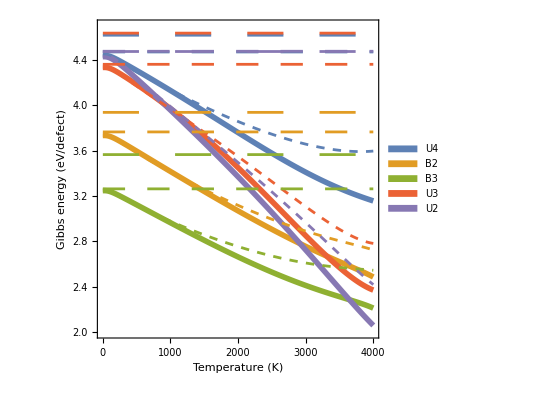

```mathematica
GraphicsGrid[{{Show[G1],
Show[{G2,G1a}]},{
Show[{G3,G2a,G1a}],
Show[{G4,G3a,G2a,G1a}]}},ImageSize->1200]
```

```mathematica
(*T_Kelvin FREN_1126_eVperD FREN_129_eVperD FREN_142_eVperD FREN_174_eVperD FREN_70_eVperD*)

(*1=1126=U4, 2=129=B2, 3=142=B3, 4=174=U3,5=70=U2 *)
```

```mathematica
(*T_Kelvin FREN_1126_eVperD FREN_129_eVperD FREN_142_eVperD FREN_174_eVperD FREN_70_eVperD*)
```

```mathematica
gibbsData=FFEdata[[4]];
mB3=24;
mB2=24;
mU2=3;
mU3=12;
mU4=12;
temperature=Transpose[gibbsData][[1]];
gibbsU4=Transpose[gibbsData][[2]];
gibbsB2=Transpose[gibbsData][[3]];
gibbsB3=Transpose[gibbsData][[4]];
gibbsU3=Transpose[gibbsData][[5]];
gibbsU2=Transpose[gibbsData][[6]];

(*1126=U4, 129=B2, 142=B3, 174=U3, 70=U2*)
```

```mathematica
Exp[-4/(K2eV*300)]
```

6.35259×10^-68

ListLinePlot::prng: Value of option PlotRange -> {Auto,{1/1000000000000000000000000000000000000000000000000000000000000,1/100000000000000000000000000000000000000000000000000}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

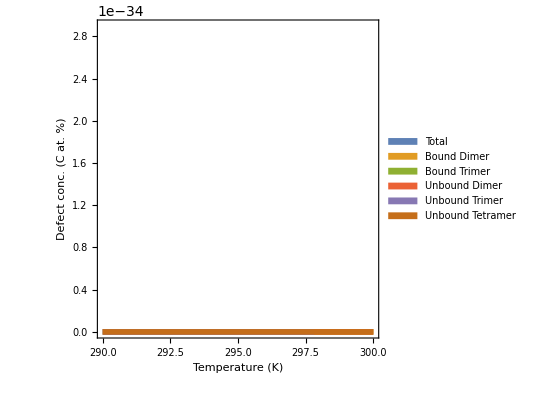

```mathematica
upper=300;
lower=290;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]};
concB3=Transpose@{rangeT,100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]};
concU2=Transpose@{rangeT,100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]};
concU3=Transpose@{rangeT,100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]};
concU4=Transpose@{rangeT,100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]};
concTotal=Transpose@{rangeT,Flatten@Transpose[{Transpose[concB2][[2]]+Transpose[concB3][[2]]+Transpose[concU2][[2]]+Transpose[concU3][[2]]+Transpose[concU4][[2]]}]};


p7=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotStyle->Thickness[0.01],Filling->Bottom,FrameStyle->Directive[Thickness[0.01]],FillingStyle->Opacity[0.09],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["Temperature (K)",18,Black],Style["Defect conc. (C at. %)",18,Black]},Frame->True,ImageSize->400,PlotLegends->Placed[SwatchLegend[{Style["Total",18,Black],Style["Bound Dimer",18,Black],Style["Bound Trimer",18,Black],Style["Unbound Dimer",18,Black],Style["Unbound Trimer",18,Black],Style["Unbound Tetramer",18,Black]}],{0.3,0.75}],AspectRatio->1,PlotRange->{Auto,{10^-60,10^-50}}]
```

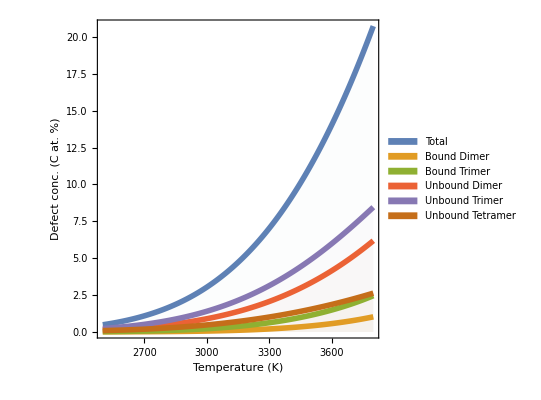

```mathematica
upper=3800;
lower=2500;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]};
concB3=Transpose@{rangeT,100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]};
concU2=Transpose@{rangeT,100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]};
concU3=Transpose@{rangeT,100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]};
concU4=Transpose@{rangeT,100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]};
concTotal=Transpose@{rangeT,Flatten@Transpose[{Transpose[concB2][[2]]+Transpose[concB3][[2]]+Transpose[concU2][[2]]+Transpose[concU3][[2]]+Transpose[concU4][[2]]}]};


p5=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotStyle->Thickness[0.01],Filling->Bottom,FrameStyle->Directive[Thickness[0.01]],FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["Temperature (K)",18,Black],Style["Defect conc. (C at. %)",18,Black]},Frame->True,ImageSize->400,PlotLegends->Placed[SwatchLegend[{Style["Total",18,Black],Style["Bound Dimer",18,Black],Style["Bound Trimer",18,Black],Style["Unbound Dimer",18,Black],Style["Unbound Trimer",18,Black],Style["Unbound Tetramer",18,Black]}],{0.3,0.75}],AspectRatio->1,PlotRange->All]
```

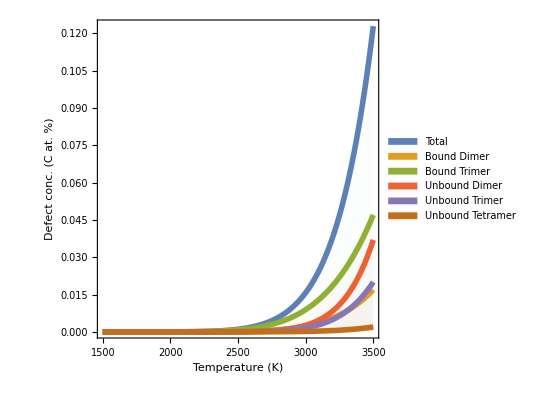

```mathematica
upper=3500;
lower=1500;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];

concB2=Transpose@{rangeT,100*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]};
concB3=Transpose@{rangeT,100*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]};
concU4=Transpose@{rangeT,100*Exp[-(rangeGibbsU4)/(K2eV*rangeT)]};

concU2=Transpose@{rangeT,100*Exp[-(rangeGibbsU2)/(K2eV*rangeT)]};
concU3=Transpose@{rangeT,100*Exp[-(rangeGibbsU3)/(K2eV*rangeT)]};


concTotal=Transpose@{rangeT,Flatten@Transpose[{Transpose[concB2][[2]]+Transpose[concB3][[2]]+Transpose[concU2][[2]]+Transpose[concU3][[2]]+Transpose[concU4][[2]]}]};
p6=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotStyle->Thickness[0.01],Filling->Bottom,FrameStyle->Directive[Thickness[0.01]],FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["Temperature (K)",18,Black],Style["Defect conc. (C at. %)",18,Black]},Frame->True,ImageSize->400,PlotLegends->Placed[SwatchLegend[{Style["Total",18,Black],Style["Bound Dimer",18,Black],Style["Bound Trimer",18,Black],Style["Unbound Dimer",18,Black],Style["Unbound Trimer",18,Black],Style["Unbound Tetramer",18,Black]}],{0.3,0.75}],AspectRatio->1,PlotRange->All]
```

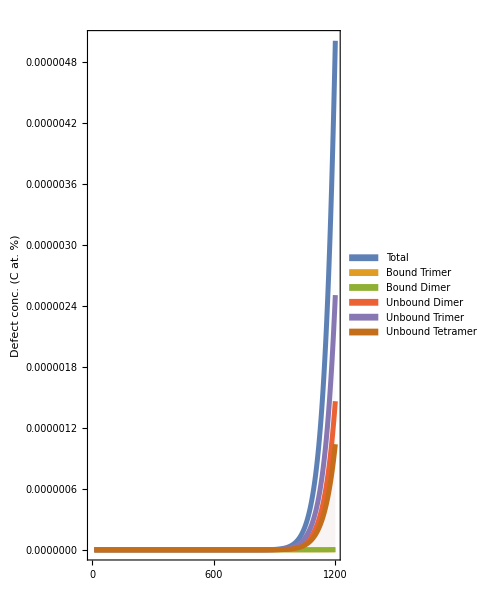

```mathematica
upper=1200;
lower=10;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]};
concB3=Transpose@{rangeT,100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]};
concU2=Transpose@{rangeT,100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]};
concU3=Transpose@{rangeT,100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]};
concU4=Transpose@{rangeT,100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]};
concTotal=Transpose@{rangeT,Flatten@Transpose[{Transpose[concB2][[2]]+Transpose[concB3][[2]]+Transpose[concU2][[2]]+Transpose[concU3][[2]]+Transpose[concU4][[2]]}]};
p1=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotStyle->Thickness[0.01],Filling->Bottom,FrameStyle->Directive[Thickness[0.01]],FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["",18,Black],Style["Defect conc. (C at. %)",18,Black]},Frame->True,ImageSize->360,PlotLegends->Placed[SwatchLegend[{Style["Total",18,Black],Style["Bound Trimer",18,Black],Style["Bound Dimer",18,Black],Style["Unbound Dimer",18,Black],Style["Unbound Trimer",18,Black],Style["Unbound Tetramer",18,Black]}],{0.4,0.80}],AspectRatio->1.7,PlotRange->All,FrameTicks->{{Automatic,None},{{0,600,1200},None}}]
```

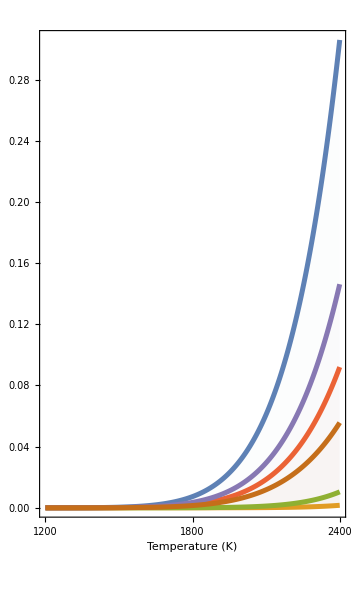

```mathematica
upper=2400;
lower=1200;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]};
concB3=Transpose@{rangeT,100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]};
concU2=Transpose@{rangeT,100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]};
concU3=Transpose@{rangeT,100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]};
concU4=Transpose@{rangeT,100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]};
concTotal=Transpose@{rangeT,Flatten@Transpose[{Transpose[concB2][[2]]+Transpose[concB3][[2]]+Transpose[concU2][[2]]+Transpose[concU3][[2]]+Transpose[concU4][[2]]}]};
p2=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotStyle->Thickness[0.01],Filling->Bottom,FrameStyle->Directive[Thickness[0.01]],FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["Temperature (K)",18,Black],Style["",18,Black]},Frame->True,ImageSize->360,AspectRatio->1.7,PlotRange->All,FrameTicks->{{Automatic,None},{{1200,1800,2400},None}}]
```

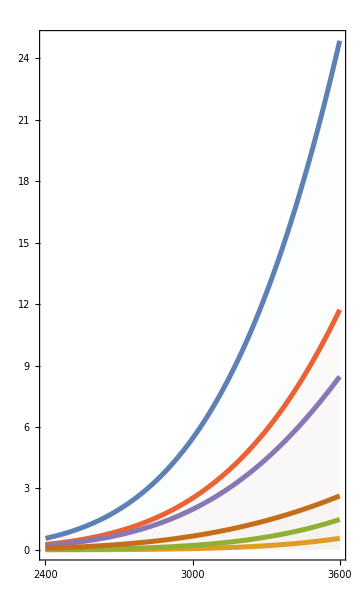

```mathematica
upper=3600;
lower=2400;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]};
concB3=Transpose@{rangeT,100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]};
concU2=Transpose@{rangeT,100*mB3^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]};
concU3=Transpose@{rangeT,100*mB3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]};
concU4=Transpose@{rangeT,100*mB3^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]};
concTotal=Transpose@{rangeT,Flatten@Transpose[{Transpose[concB2][[2]]+Transpose[concB3][[2]]+Transpose[concU2][[2]]+Transpose[concU3][[2]]+Transpose[concU4][[2]]}]};
p3=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotStyle->Thickness[0.01],Filling->Bottom,FrameStyle->Directive[Thickness[0.01]],FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["",18,Black],Style["",18,Black]},Frame->True,ImageSize->360,AspectRatio->1.7,PlotRange->All,FrameTicks->{{Automatic,None},{{2400,3000,3600},None}}]
```

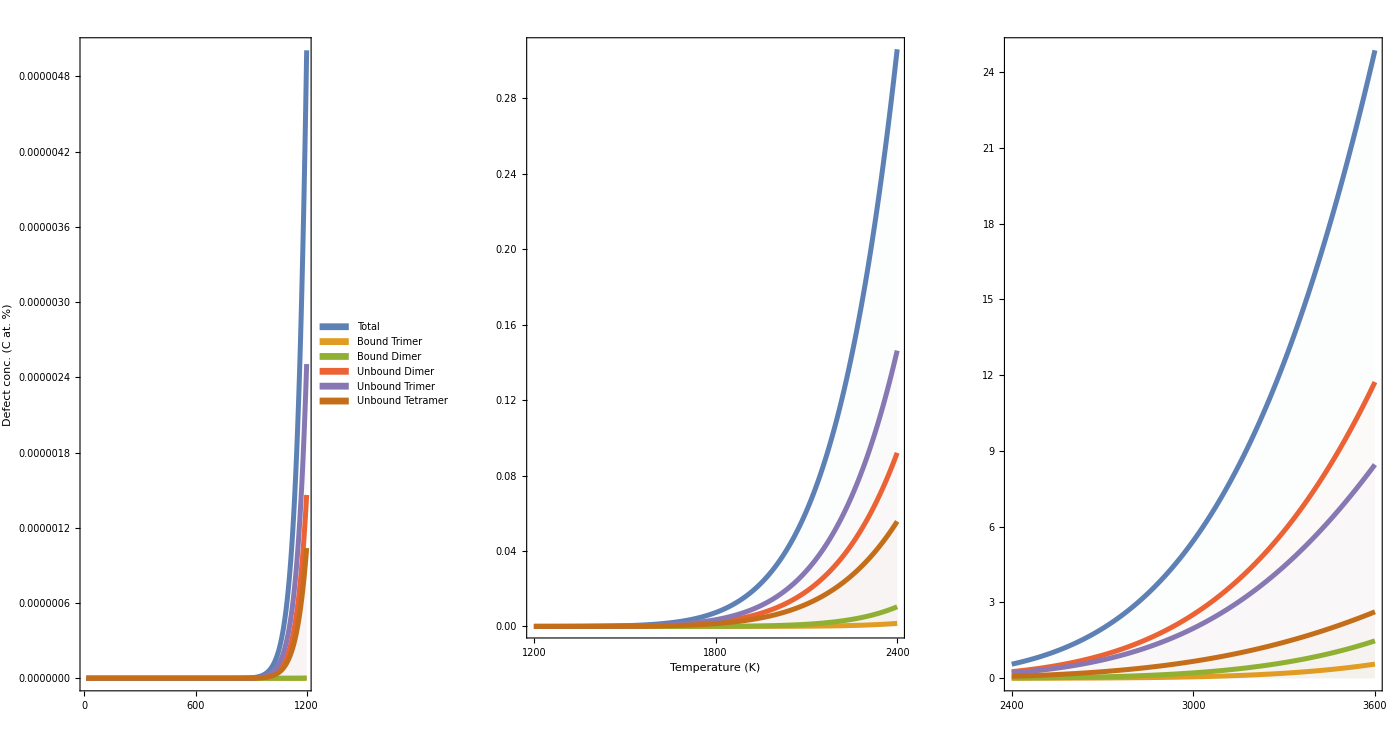

```mathematica
GraphicsGrid[{{p1,p2,p3}},ImageSize->1400]
```